#### Iniziamo con un reminder sulla rappresentazione del fascio

```mathematica
(*  Partiamo dalla matrice sigma (a meno dell'emittanza fattorizzata)  *)
MT={{γ,α},{α,β}};
Print["Twiss Matrix -> ",MatrixForm[MT]]
Print["Beam Quadratic Form -> ",Simplify[{x,xp}.MT.{x,xp}]//TraditionalForm]

(* e definiamo la matrice di normalizzazione con la sua inversa *)

NM={{1/Sqrt[β],0},{α/Sqrt[β],Sqrt[β]}};
NMI={{Sqrt[β],0},{-α/Sqrt[β],1/Sqrt[β]}};
Print["Normalization Matrix         -> ",MatrixForm[NM]]
Print["Inverse Normalization Matrix -> ",MatrixForm[NMI]]
Print["Product Verification         -> ",MatrixForm[NMI.NM]]

(* 
le coordinate normalizzate sono {XN,YN}=NM.{x,y}. Verifichiamo che l'ellissi diventa un cerchio 
2 x y α+y^2 β+x^2 γ -> XN^2+YN^2 
*)

Simplify[{XN,XPN}.Transpose[NMI].MT.NMI.{XN,XPN}]/.γ->(1+α^2)/β

 (*
a questo punto data una ampiezza ottengo le coordinate normalizzate da coseno e seno della fase 
e e coordinate reali con la matrice inversa. Per una ampiezza A (= Sqrt[emittance]) 
*)

NMI.{A Cos[θ], A Sin[θ]}
```

Twiss Matrix -> (γ | α
α | β)

Beam Quadratic Form -> γ x^2+2 α x xp+β xp^2

Normalization Matrix         -> (1/(√β) | 0
α/(√β) | √β)

Inverse Normalization Matrix -> (√β | 0
-α/(√β) | 1/(√β))

Product Verification         -> (1 | 0
0 | 1)

XN^2+XPN^2

{{{0.-0.00238324 √β,0.-0.000162519 √β,0.+0.000934882 √β,0.-0.000443257 √β,0.},998,{0.+0.00291463 √β,0.-0.0000344389 √β,0.+1,0.-23 √β,0.}},{1}}
 |  |  |  |

#### definiamo i parametri del fascio Al setto elettrostatico di estrazione abbiamo

```mathematica
7.14/5
```

1.428

```mathematica
Npart = 1000;

epsxrms=7 10^-6;
epsx=5epsxrms;
betx=10;
alfx=0;
gamx=(1+alfx^2)/betx;
Dx=0.0;
Dxp=0.0;

NMIx={{Sqrt[betx],0},{-alfx/Sqrt[betx],1/Sqrt[betx]}};

epsyrms=7 10^-6;
epsy=5epsyrms;
bety=10;
alfy=0;
gamy=(1+alfy^2)/bety;
Dy=0.0;
Dyp=0.0;

NMIy={{Sqrt[bety],0},{-alfy/Sqrt[bety],1/Sqrt[bety]}};
```

### Generation test

#### Generiamo la distribuzione radiale per un fascio gaussiano Define radial distribution and generate value set. Define centered and with unit sigma.

Piecewise[{{ⅇ^(-x^2/2) x, x>0}, {0, True}}]

{0.393469,0.5,0.864665,0.917915,0.988891,0.999996}

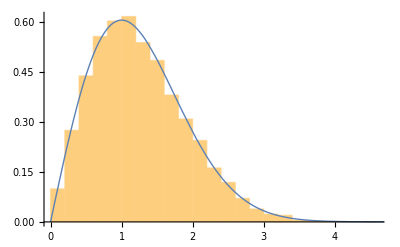

```mathematica
(*
𝒟=ProbabilityDistribution[2π (x-μ)/(2π σ^2) Exp[-(x-μ)^2/(2σ^2)]/.{μ->0,σ->1},{x,μ,Infinity}];
*)
𝒟=ProbabilityDistribution[2π x/(2π σ^2) Exp[-(x)^2/(2σ^2)]/.{σ->1},{x,0,Infinity}];

PDF[𝒟,x]

Integrate[PDF[𝒟,x],{x,0,#}]&/@{1,Sqrt[Log[4]],2,Sqrt[5],3,5}//N

amplitudex=RandomVariate[𝒟,10^4];
amplitudey=RandomVariate[𝒟,10^4];

Show[
Histogram[amplitudex,20,"ProbabilityDensity"],
Plot[PDF[𝒟,x]/.{σ->1},{x,0,9},PlotStyle->Thick]]
```

#### From radial distribution generate position in normalised phase space. Amplitude goes with Sqrt[RMS emittance]

```mathematica
coorx={};
Do[θ=RandomReal[{0,2π}];AppendTo[coorx,amplitudex[[n]]*Sqrt[epsxrms]*NMIx.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudex]}]

coory={};
Do[θ=RandomReal[{0,2π}];AppendTo[coory,amplitudey[[n]]*Sqrt[epsyrms]*NMIy.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudey]}]
```

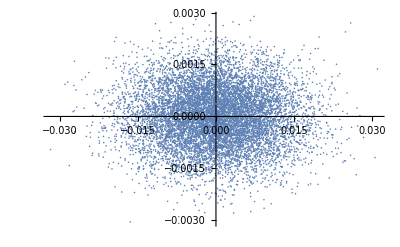

```mathematica
ListPlot[coorx]
```

#### Passiamo alla generazione di un fascio omogeneo 2D

Piecewise[{{(2 x)/5, 0<x<√5}, {0, True}}]

{0.2,0.277259,0.8,1.,1.,1.}

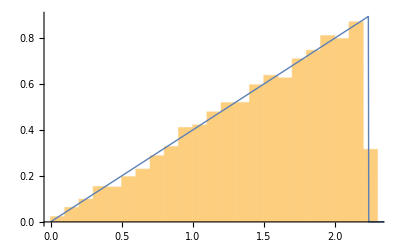

```mathematica
𝒟=ProbabilityDistribution[2π x/(π R^2),{x,0,R}]/.{R->Sqrt[5]};

PDF[𝒟,x]

Integrate[PDF[𝒟,x],{x,0,#}]&/@{1,Sqrt[Log[4]],2,Sqrt[5],3,5}//N

amplitudex=RandomVariate[𝒟,10^4];
amplitudey=RandomVariate[𝒟,10^4];

Show[
Histogram[amplitudex,20,"ProbabilityDensity"],
Plot[PDF[𝒟,x]/.{σ->1},{x,0,9},PlotStyle->Thick]]
```

#### From radial distribution generate position in normalised phase space. Amplitude goes with Sqrt[RMS emittance]

```mathematica
coorx={};
Do[θ=RandomReal[{0,2π}];AppendTo[coorx,amplitudex[[n]]*Sqrt[epsxrms]*NMIx.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudex]}]

coory={};
Do[θ=RandomReal[{0,2π}];AppendTo[coory,amplitudey[[n]]*Sqrt[epsyrms]*NMIy.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudey]}]
```

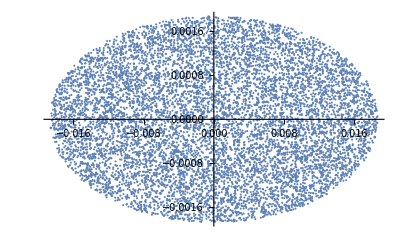

```mathematica
ListPlot[coorx]
```

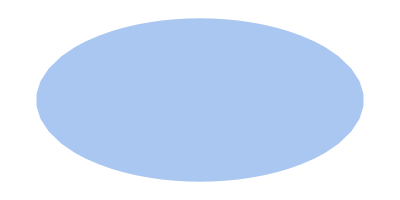

```mathematica
ℛ=ImplicitRegion[(x/2)^2+y^2≤1,{x,y}];
Region[ℛ]
```

```mathematica
pts=RandomPoint[ℛ,5000];
```

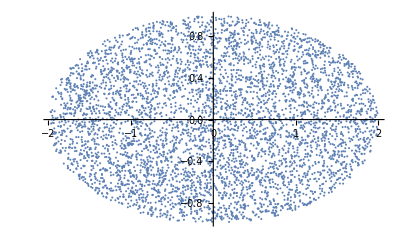

```mathematica
ListPlot[pts]
```

```mathematica
DirichletDistribution
```

DirichletDistribution

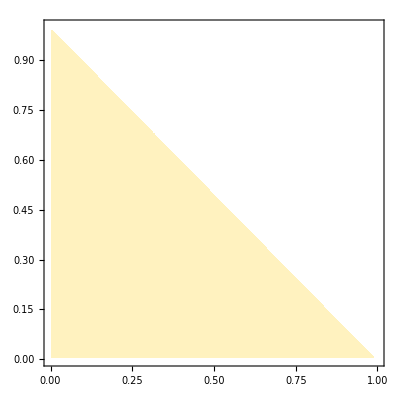

```mathematica
ContourPlot[PDF[DirichletDistribution[{ 1,1,1}],{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y<1]]
```

### Generate Flat/Gaussian beam

Genero (N * 1/0.91) particelle distribuite in modo gaussiano in modo da averne 
N dentro a una emittanza 5 e_rms 
(dentro a 5 e_rms cade il 91.79 delle particelle generate)

#### Generiamo una distribuzione gaussiana in y e piatta in x (~MTI) Genero anche una distribuzione uniforme in Dp/p

Piecewise[{{ⅇ^(-x^2/2) x, x>0}, {0, True}}]

{0.393469,0.5,0.864665,0.917915}

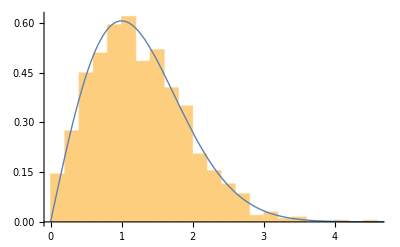

```mathematica
𝒟𝒢=ProbabilityDistribution[2π x/(2π σ^2) Exp[-(x)^2/(2σ^2)]/.{σ->1},{x,0,Infinity}];

PDF[𝒟𝒢,x]

Integrate[PDF[𝒟𝒢,x],{x,0,#}]&/@{1,Sqrt[Log[4]],2,Sqrt[5]}//N

amplitudey=RandomVariate[𝒟𝒢,Npart];

Show[
Histogram[amplitudey,20,"ProbabilityDensity"],
Plot[PDF[𝒟𝒢,x]/.{σ->1},{x,0,9},PlotStyle->Thick]]
```

Piecewise[{{(2 x)/5, 0<x<√5}, {0, True}}]

{0.2,0.277259,0.8,1.,1.,1.}

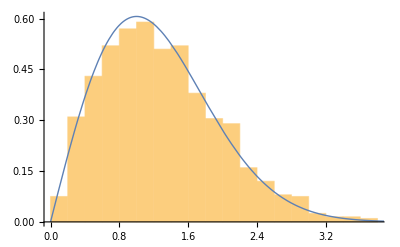

```mathematica
𝒟ℱ=ProbabilityDistribution[2π x/(π R^2),{x,0,R}]/.{R->Sqrt[5]};

PDF[𝒟ℱ,x]

Integrate[PDF[𝒟ℱ,x],{x,0,#}]&/@{1,Sqrt[Log[4]],2,Sqrt[5],3,5}//N

(*amplitudex=RandomVariate[𝒟ℱ,3 10^4];*)
amplitudex=RandomVariate[𝒟𝒢,Npart];

Show[
Histogram[amplitudex,20,"ProbabilityDensity"],
Plot[PDF[𝒟𝒢,x]/.{σ->1},{x,0,9},PlotStyle->Thick]]
```

```mathematica
coorx={};
Do[θ=RandomReal[{0,2π}];AppendTo[coorx,amplitudex[[n]]*Sqrt[epsxrms]*NMIx.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudex]}]

coory={};
Do[θ=RandomReal[{0,2π}];AppendTo[coory,amplitudey[[n]]*Sqrt[epsyrms]*NMIy.{Cos[θ], Sin[θ]}],{n,1,Length[amplitudey]}]
```

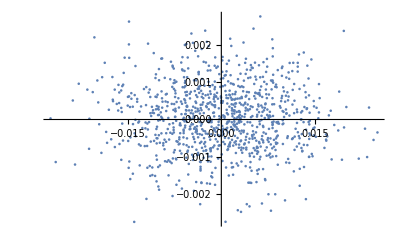

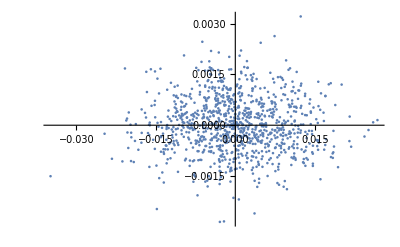

```mathematica
ListPlot[coorx]
ListPlot[coory]
```

UniformDistribution[{0,0}]

UniformDistribution::lss: Parameter 0 at position {1,1} in UniformDistribution[{0,0}] is expected to be less than 0.

PDF[UniformDistribution[{0,0}],x]

UniformDistribution::lss: Parameter 0 at position {1,1} in UniformDistribution[{0,0}] is expected to be less than 0.

UniformDistribution::lss: Parameter 0. at position {1,1} in UniformDistribution[{0.,0.}] is expected to be less than 0..

UniformDistribution::lss: Parameter 0 at position {1,1} in UniformDistribution[{0,0}] is expected to be less than 0.

General::stop: Further output of UniformDistribution::lss will be suppressed during this calculation.

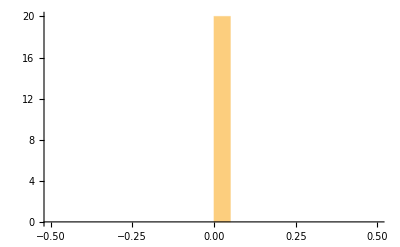

```mathematica
𝒟ℳ=UniformDistribution[{0,0}]

PDF[𝒟ℳ,x]

amplitudep=RandomVariate[𝒟ℳ,Npart];

Show[
Histogram[amplitudep,20,"ProbabilityDensity"],
Plot[PDF[𝒟ℳ,x]/.{σ->1},{x,-0.003,0.003},PlotStyle->Thick]]
```

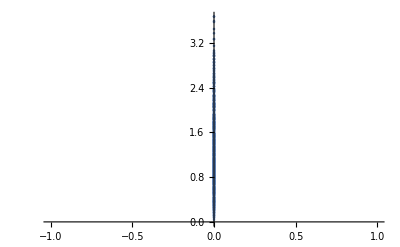

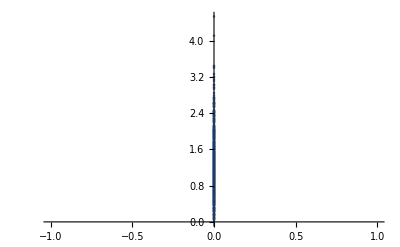

```mathematica
ListPlot[Transpose[{amplitudep,amplitudex}]]
ListPlot[Transpose[{amplitudep,amplitudey}]]
```

```mathematica
Ax=Sqrt[gamx*#[[1]]^2+2*alfx*#[[1]]*#[[2]]+betx*#[[2]]^2]&/@coorx;
```

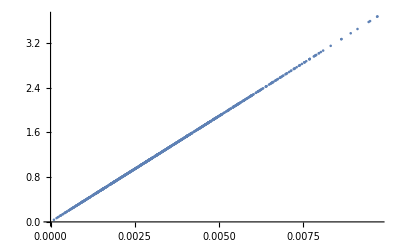

```mathematica
ListPlot[Transpose[{Ax,amplitudex}]]
```

```mathematica
coorx[[1;;3]]
```

{{0.00466641,-0.00113585},{0.00968867,0.0013731},{0.00956925,0.000490464}}

#### Check statistical quantities from distribution

```mathematica
x2=Mean[coorx[[;;,1]]^2];
xp2=Mean[coorx[[;;,2]]^2];
xxp=Mean[coorx[[;;,1]]*coorx[[;;,2]]];

y2=Mean[coory[[;;,1]]^2];
yp2=Mean[coory[[;;,2]]^2];
yyp=Mean[coory[[;;,1]]*coory[[;;,2]]];
```

```mathematica
epsStatx=Sqrt[x2*xp2-xxp^2]
betaStatx=x2/Sqrt[x2*xp2-xxp^2]
alfaStatx=-xxp/Sqrt[x2*xp2-xxp^2]
epsxrms
betx
alfx

epsStaty=Sqrt[y2*yp2-yyp^2]
betaStaty=y2/Sqrt[y2*yp2-yyp^2]
alfaStaty=-yyp/Sqrt[y2*yp2-yyp^2]
epsyrms
bety
alfy
```

7.4264×10^-6

9.75315

0.0297339

7/1000000

10

0

6.98514×10^-6

10.4707

0.00985744

7/1000000

10

0

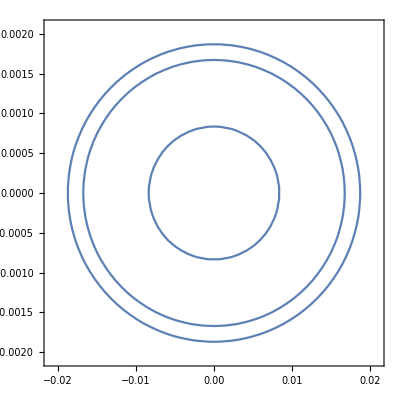

```mathematica
ContourPlot[gamx*x^2+2*alfx*x*xp+betx*xp^2=={epsxrms,4epsxrms,5epsxrms},{x,-2.5*Sqrt[epsxrms*betx],2.5*Sqrt[epsxrms*betx]},{xp,-2.5*Sqrt[epsxrms*gamx],2.5*Sqrt[epsxrms*gamx]}]
```

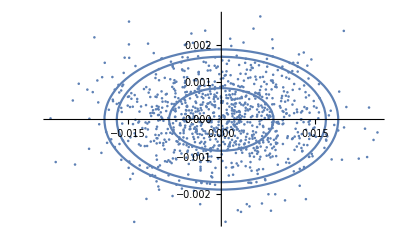

```mathematica
Show[ListPlot[coorx],ContourPlot[gamx*x^2+2*alfx*x*xp+betx*xp^2=={epsxrms,4epsxrms,5epsxrms},{x,-2.5*Sqrt[epsxrms*betx],2.5*Sqrt[epsxrms*betx]},{xp,-2.5*Sqrt[epsxrms*gamx],2.5*Sqrt[epsxrms*gamx]}]]
```

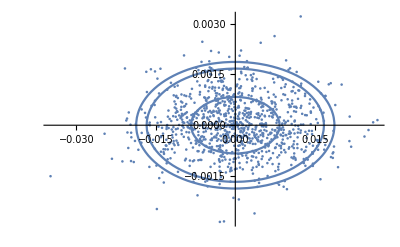

```mathematica
Show[ListPlot[coory],ContourPlot[gamy*y^2+2*alfy*y*yp+bety*yp^2=={epsyrms,4epsyrms,5epsyrms},{y,-2.5*Sqrt[epsyrms*bety],2.5*Sqrt[epsyrms*bety]},{yp,-2.5*Sqrt[epsyrms*gamy],2.5*Sqrt[epsyrms*gamy]}]]
```

```mathematica
s1=Select[coory,gamy*#[[1]]^2+2*alfy*#[[1]]*#[[2]]+bety*#[[2]]^2<5*epsyrms &];
Length[s1]
Length[coory]
```

918

1000

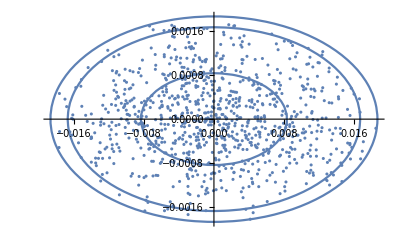

```mathematica
Show[ListPlot[s1],ContourPlot[gamy*y^2+2*alfy*y*yp+bety*yp^2=={epsyrms,4epsyrms,5epsyrms},{y,-2.5*Sqrt[epsyrms*bety],2.5*Sqrt[epsyrms*bety]},{yp,-2.5*Sqrt[epsyrms*gamy],2.5*Sqrt[epsyrms*gamy]}],PlotRange->All]
```

```mathematica
f[x_,n_]:=StringTake["                   "<>ToString[Row[{PaddedForm[MantissaExponent[N[x]][[1]],n,NumberPadding->{" ","0"}],"E",MantissaExponent[x][[2]]}]],-19]

f[-π/1000,{10,10}]
```

-0.3141592654E-2

{{0.00466641,-0.00113585,0.00805012,0.0014196,0.},{0.00968867,0.0013731,-0.0000573915,-0.00130329,0.},{0.00956925,0.000490464,-0.00056454,-0.000794559,0.},{0.00812885,-0.0000756169,0.0133913,-0.0006395,0.},{-0.00844435,-0.00149109,-0.0123906,0.000184945,0.},{-0.00719699,0.00100789,0.00862697,-0.000679531,0.},{-0.000441686,-0.000147321,0.0129244,-0.000998998,0.},{-0.0120505,0.000384262,-0.000609588,-0.000107753,0.},{0.0229919,-0.000244772,0.00116923,-0.000338472,0.},{-0.0149815,0.000370849,0.00397425,-0.0000228267,0.}}

Part::partw: Part 9999 of {{0.00466641,-0.00113585,0.00805012,0.0014196,0.},{0.00968867,0.0013731,-0.0000573915,-0.00130329,0.},«8»,«990»} does not exist.

{{0.00466641,-0.00113585,0.00805012,0.0014196,0.},{0.00968867,0.0013731,-0.0000573915,-0.00130329,0.},{0.00956925,0.000490464,-0.00056454,-0.000794559,0.},{0.00812885,-0.0000756169,0.0133913,-0.0006395,0.},{-0.00844435,-0.00149109,-0.0123906,0.000184945,0.},{-0.00719699,0.00100789,0.00862697,-0.000679531,0.},{-0.000441686,-0.000147321,0.0129244,-0.000998998,0.},{-0.0120505,0.000384262,-0.000609588,-0.000107753,0.},{0.0229919,-0.000244772,0.00116923,-0.000338472,0.},{-0.0149815,0.000370849,0.00397425,-0.0000228267,0.},{-0.00130195,0.000176292,-0.00769673,0.000664062,0.},{0.0037986,0.000146679,-0.000178946,0.000623734,0.},{0.00407438,-0.00225978,0.00320851,0.00131148,0.},{0.0029,-0.000310336,-0.0136395,-0.000248873,0.},{-0.00737432,0.0000737836,-0.00160183,0.00108296,0.},{0.00665444,0.00113819,-0.012972,-0.000110553,0.},{-0.0186554,0.00151327,0.00668573,-0.00097389,0.},{0.00703952,-0.00161964,-0.00361723,0.000723378,0.},{-0.0107852,0.000170041,0.00300827,-0.000466894,0.},{-0.0160105,0.000309297,0.00899453,-0.0000630089,0.},{0.007268,-0.000743332,0.0086803,-0.0000999947,0.},{0.00467433,0.00132063,-0.00568299,0.00117386,0.},{0.00207792,0.00021658,0.00302746,-0.00104317,0.},{0.00499728,-0.000514323,-0.0109142,0.000396541,0.},{0.00776734,0.000205153,-0.00522873,-0.0000969676,0.},{0.00773376,0.00010646,0.00211938,-0.000230542,0.},{0.00285155,0.00145533,-0.012851,4.46236×10^-6,0.},{-0.00176779,-0.0000293113,0.00402416,0.00136534,0.},{-0.0165047,0.000239629,-0.0091377,0.000219882,0.},{-0.00393785,-0.000316642,0.00179072,0.000652298,0.},{-0.00170545,-0.000847784,-0.00565603,-0.0016672,0.},{0.00658607,0.000321327,0.012936,-0.00111914,0.},{-0.0103965,-0.000961568,-0.00304054,-0.00104109,0.},{0.00980629,0.000226106,0.00703504,-0.00114804,0.},{0.00659079,0.000203371,-0.0111058,-0.000454711,0.},{-0.00734692,0.000285434,-0.00563807,-0.000418361,0.},{0.00294236,-0.0000236065,-0.00465383,-0.000435489,0.},{0.00591055,0.000400338,-0.00434291,0.00108109,0.},{-0.00384561,0.00060167,0.00632667,0.000812545,0.},{-0.00733044,0.000222063,0.00228815,-0.000974321,0.},{-0.00332623,-0.00136179,-0.0029299,0.000435025,0.},{0.0106274,-0.000447162,-0.0114743,0.00070132,0.},{-0.00362475,0.00120882,0.00102563,0.0000850711,0.},{-0.00552207,-0.000064986,-0.00553638,0.000743341,0.},{0.00464596,0.00112126,0.00761916,-0.000655689,0.},{-0.00372528,-0.000890148,-0.0140676,-0.00035299,0.},{-0.00332573,-0.00126193,-0.000994466,0.000714715,0.},{0.00257983,0.0000608972,-0.00932369,-0.000991284,0.},{0.00141849,-0.00060995,0.0022273,-0.000348529,0.},{-0.0138641,0.000651707,-0.0100288,0.000163582,0.},{-0.00873529,0.00068381,0.00129041,0.0000440453,0.},{-0.0120101,-0.000462438,0.00888409,0.000050897,0.},{0.00119787,-0.000343182,-0.000843322,0.00064658,0.},{0.00969593,0.00116491,-0.00850302,0.000920689,0.},{-0.0103579,-0.000499051,0.00313466,-0.0013223,0.},{0.0105743,0.000725782,0.00143229,0.000351966,0.},{-0.00733299,0.000697674,-0.00371119,-0.00013022,0.},{-0.00434921,-0.00024867,-0.00450993,0.00168283,0.},{-0.0170365,-0.000735208,-0.00597626,-0.000201686,0.},{-0.00960789,0.0000718081,0.00379158,-0.000128251,0.},{0.0122305,0.0015122,-0.0122313,-0.000977061,0.},{0.00762547,-0.000249962,-0.0161249,-1.23529×10^-6,0.},{0.0125187,-0.00049893,0.00894226,-0.000546637,0.},{0.00100498,-0.0000847322,0.00604801,0.000428177,0.},{-0.00317546,0.000249009,0.0131866,0.000299229,0.},{-0.00331253,0.000392516,0.00239222,-0.000121572,0.},{-0.00760144,-0.000345862,0.0113298,-7.70326×10^-6,0.},{0.00728814,0.000570019,-0.0116771,-0.0000569543,0.},{-0.00330146,0.000305007,0.000439302,0.000521461,0.},{0.0195986,0.00236418,-0.00794671,0.00032739,0.},{-0.00848439,0.0000417242,-0.0146747,0.0000695754,0.},{0.00815432,0.00213902,0.0127936,-0.00109391,0.},{0.00570339,0.0000771476,0.0167191,0.000124649,0.},{0.0036566,-0.000664819,-0.00569156,0.00043271,0.},{0.0104523,0.000165658,0.00117946,-0.000477304,0.},{0.00614802,-0.000124622,-0.00511549,0.0016131,0.},{0.00180757,-0.000252219,0.00331785,-0.000551958,0.},{-0.0128442,0.000348196,0.00640814,-0.00102053,0.},{-0.0103294,0.00035981,-0.00381077,0.0011111,0.},{0.0049719,-0.000458997,0.00229348,0.000103987,0.},{0.00388445,0.000238142,-0.00197228,0.000691986,0.},{0.00359397,-0.000299434,-0.00343448,-0.000460871,0.},{0.0132055,-0.000676965,0.00389846,-0.0000716243,0.},{0.0106722,0.000511782,0.0100443,0.00163763,0.},{0.00666371,-0.000169699,-0.000237415,4.10673×10^-6,0.},{0.0099054,0.000857611,0.0129845,-0.000788209,0.},{-0.0173289,0.000488459,-0.0140007,-0.000344154,0.},{0.000757201,-0.00128125,-0.00234079,0.0012886,0.},{-0.00929247,-0.000691353,0.00322937,0.00101403,0.},{-0.000474034,-0.000416036,-0.00123584,0.000481411,0.},{-0.00242379,0.000353994,0.00218047,0.000499909,0.},{-0.00104463,0.00101249,0.00661567,-0.000257461,0.},{-0.00297627,0.000682735,-0.00304877,0.000165769,0.},{-0.0211648,-0.000781943,0.00169615,0.0017187,0.},{0.00399564,0.000636301,-0.0143922,0.000938765,0.},{0.0108826,-0.00115883,-0.000172837,0.00053125,0.},{0.00421874,0.000400333,0.0218637,-0.000635176,0.},{0.0116015,-0.00138397,0.0044923,-0.00158215,0.},{0.00791466,-0.000664431,0.00833648,-0.0000993421,0.},{0.00307525,-0.000579892,-0.00291185,-0.00285663,0.},{0.00588445,-0.000864108,0.0115842,0.00157437,0.},{0.0132957,0.000332758,-0.00598208,0.000028206,0.},{-0.0103905,-0.000252964,-0.0111832,0.000839801,0.},{0.00572685,-0.000200385,-0.000281851,0.000131344,0.},{-0.011834,-0.000108089,-0.00723967,0.000335418,0.},{-0.0028889,0.000567886,-0.017718,-0.000516874,0.},{-0.0117559,-0.00026604,-0.00811699,-0.0000836823,0.},{0.00757429,-0.000597063,-0.0134536,-0.000847219,0.},{-0.0054926,0.000645585,0.0147555,0.000522259,0.},{0.00884608,0.000861757,-0.00117591,0.000854948,0.},{0.00125937,-0.0000482252,0.0109313,-0.000981656,0.},{-0.0104594,0.000271805,-0.00568925,0.000808721,0.},{-0.0000208323,0.000450581,-0.00498685,0.0000196343,0.},{0.00804457,0.000803495,-0.0201017,0.000376929,0.},{-0.0115632,-0.0000681977,-0.00182233,-0.000523411,0.},{0.000800239,0.000647559,-0.00206707,0.00060966,0.},{-0.00427313,0.000069623,-0.00295675,-0.00173777,0.},{0.00121064,0.0015711,0.0160263,0.000455715,0.},{-0.0138701,-0.000369087,0.00291526,0.0000239812,0.},{0.00278796,0.0000642096,-0.00255785,0.00132037,0.},{-0.00494846,-0.00025213,-0.00118301,-0.000367257,0.},{0.0018166,0.000537561,-0.00371166,0.000552486,0.},{-0.0100379,0.000338119,0.00994421,0.000127291,0.},{0.0081877,0.000568088,-0.00474607,0.00150669,0.},{-0.00596826,0.0011292,-0.00976466,-0.0000722749,0.},{0.000889132,0.00148479,-0.0107574,-0.000582289,0.},{0.0101913,-0.00215824,-0.00981221,0.0000846888,0.},{0.0140584,-0.000996143,-0.00190636,-0.000487524,0.},{-0.00114557,0.0000828328,0.00356268,-0.000810965,0.},{-0.0100012,-0.000418877,0.00828558,-0.00088759,0.},{-0.00390342,-0.000181724,-0.000409953,-0.0000503959,0.},{0.00246093,0.00170106,0.0146412,-0.00113598,0.},{0.0167629,-0.000536639,-0.000113818,-0.000250239,0.},{-0.00308313,0.00108131,-0.00600914,-0.000781842,0.},{0.0052645,0.000948626,-0.00292891,-0.00161388,0.},{-0.00313161,0.000603078,0.0043295,0.000310216,0.},{0.00667049,-0.000559241,0.00498184,-0.000998584,0.},{-0.00905075,0.00111107,0.000925657,-0.000346005,0.},{0.00329585,0.0000845695,0.00332713,0.00107923,0.},{0.000169654,-0.00032377,-0.018293,-0.000725074,0.},{-0.000888406,-0.000326197,0.00912379,-0.00181751,0.},{-0.00574002,0.000447736,0.00179446,0.000321977,0.},{0.000830367,0.000575232,-0.00415979,0.000015445,0.},{-0.00424696,0.000759204,0.00725909,0.00090478,0.},{0.00211177,-0.000614399,0.00605633,-0.00111984,0.},{0.00965124,0.000569603,0.00502748,-0.0000308353,0.},{-0.00488626,0.000171424,-0.004808,-0.0006548,0.},{0.00155663,-0.000203015,-0.00226715,-0.000274514,0.},{-0.009282,-0.000630865,0.00108494,0.00220726,0.},{-0.0195425,-0.000126874,-0.00295206,-0.00134951,0.},{0.00360856,0.0010364,0.0039483,-0.000754877,0.},{0.0035461,-0.000338687,-0.00035185,-0.00214611,0.},{0.00982593,-0.0000197759,-0.00393049,-0.00113459,0.},{-0.000564482,-0.000240825,0.0184957,-0.000801074,0.},{0.00119768,-0.00149521,-0.000961718,0.00104341,0.},{0.00200974,-0.000287723,0.0111777,-0.000244597,0.},{-0.000325756,0.0000860492,0.00856106,-0.000277526,0.},{-0.000299444,-0.000444306,-0.00337386,-0.000140072,0.},{0.00127055,-0.000675263,0.00402819,-0.000272979,0.},{0.00495742,-0.000162507,0.0125122,-0.000716325,0.},{0.0113835,0.000398102,-0.000339092,-0.0010856,0.},{-0.0158493,0.000890991,-0.00967368,0.00206205,0.},{-0.0146137,0.000333367,-0.0130181,-0.000429506,0.},{0.000294907,0.000109584,-0.00167172,-0.000483683,0.},{0.00603712,0.000196286,-0.0196163,-0.000356978,0.},{0.000522865,0.00117052,-0.00697043,-0.00103451,0.},{0.00285272,0.000224724,0.00879924,7.571×10^-6,0.},{0.0103951,0.000156557,0.00145678,0.0000171493,0.},{0.00972027,0.000628203,0.00429934,-0.000475876,0.},{0.0122468,-0.000340904,-0.00599329,0.00032222,0.},{-0.0129145,-0.000697746,-0.0140261,0.0000938289,0.},{0.00233967,0.000428625,-0.00184418,-0.000324656,0.},{-0.00363868,0.00125318,-0.00863696,0.000848597,0.},{-0.00613677,-1.91702×10^-6,-0.00227913,0.000886075,0.},{-0.00845818,-0.00108829,-0.00322133,0.000647058,0.},{-0.000309329,7.67798×10^-6,0.000908324,0.00084952,0.},{-0.00309998,-0.000409805,-0.0096431,0.0000671231,0.},{-0.0102013,0.000662784,0.0079498,-0.000354808,0.},{-0.0160085,-0.00107605,0.00253156,0.00088438,0.},{-0.00319962,-0.000595706,0.00823411,0.0000997249,0.},{-0.00199201,0.00143432,0.00533325,-0.0000377445,0.},{-0.00750172,0.00104869,0.00959017,0.00191596,0.},{-0.0163306,0.000721486,0.0142428,0.000406893,0.},{0.00326969,-0.000297477,-0.00773765,0.0000446589,0.},{-0.00816194,-0.000353203,-0.0069288,-0.000767888,0.},{0.00676374,-0.000346173,0.00285772,-0.000472653,0.},{0.00573408,-0.000914459,0.0170055,0.000868609,0.},{0.000979259,-0.000811844,0.00933075,0.00113416,0.},{-0.0022159,0.000421089,0.00448682,-0.00170329,0.},{0.00321692,-0.000750817,-0.00102146,-0.00101835,0.},{-0.00674452,-0.0016308,-0.011241,0.000250041,0.},{-0.00699267,-0.000594307,-0.00818163,0.00107468,0.},{-0.00356814,0.000820926,-0.00125345,0.000356203,0.},{-0.0179989,0.00025982,-0.00419926,0.00163621,0.},{0.0071686,0.00126969,-0.0176621,-0.000226788,0.},{-0.0101042,-0.00126749,-0.0111208,0.000868073,0.},{0.00179305,0.000249002,-0.00477771,0.000422007,0.},{0.00223205,0.000427191,-0.0106041,7.00696×10^-6,0.},{-0.0101255,0.000117578,0.00867464,-0.000801609,0.},{0.00595937,0.000687959,-0.0161484,0.0000771507,0.},{-0.00363925,0.0000227331,0.00730649,0.00040244,0.},{-0.00182915,0.000880884,-0.0129447,-0.0000526323,0.},{0.0020816,-0.0000590298,0.000794098,-0.00111682,0.},{-0.0113715,-0.00150396,-0.00872347,-0.000212721,0.},{0.0131594,-0.0000700688,0.018407,-0.000965662,0.},{0.00699121,-0.00159065,0.0118626,-0.0000185478,0.},{0.00283776,0.0000940082,-0.00101695,0.0010734,0.},{0.00216963,-0.000437602,-0.00186084,0.000300056,0.},{-0.0141332,-0.000122646,0.0107932,0.00128811,0.},{0.00517673,-0.000763997,-0.0040177,-0.000360326,0.},{0.0104016,0.00112032,0.0104063,-0.000345717,0.},{0.0137653,0.00143665,0.00939669,0.000894753,0.},{0.00707413,0.000427122,0.00292031,0.000243107,0.},{0.00389927,-0.000542256,-0.00169985,-0.00044807,0.},{0.0152396,0.00031234,0.00127554,0.000938944,0.},{0.00221687,-0.000144549,-0.00116369,0.000558894,0.},{-0.0114675,0.000799566,-0.00605483,-0.0000861534,0.},{0.000335047,-0.00024674,0.00502314,0.0000214908,0.},{-0.00672545,-0.00052996,-0.00367551,0.0000484257,0.},{0.00786322,-0.000505366,0.00683222,-0.000418769,0.},{-0.0043852,-0.00190338,0.0112295,0.000138152,0.},{0.0103384,0.000634491,0.0119396,-0.000109676,0.},{-0.000603531,-0.000591128,-0.00712382,-0.000766984,0.},{0.0132494,0.000907629,0.00831022,-0.000601675,0.},{0.00702377,-0.000827077,-0.0127648,-0.00100706,0.},{0.0136563,0.000279361,0.00719864,0.000312546,0.},{0.00187778,-0.00127015,0.00371655,-0.000308719,0.},{-0.00946341,0.000315271,-0.00356782,0.000407438,0.},{-0.00412786,0.000477983,0.0251384,-0.000142274,0.},{-0.00191542,-0.000463718,-0.00562449,-0.0000953712,0.},{-0.00610042,-4.11748×10^-7,-0.00308984,0.00110799,0.},{0.00623886,0.00274969,0.0136014,-0.000264568,0.},{0.00399824,-0.000752227,-0.00670103,0.000906759,0.},{0.00653528,-0.000443091,0.0108258,0.0010073,0.},{0.00712998,-0.000380442,0.0157711,-0.000514283,0.},{-0.00900723,-0.00111383,0.00511004,0.000563469,0.},{-0.00499597,-0.000188663,-0.00274222,0.000321797,0.},{0.00440857,0.000728063,-0.00346146,-0.000619483,0.},{0.00570282,-0.000726703,0.000976307,-0.000202919,0.},{0.00671112,-0.000609944,-0.0154943,-0.000431103,0.},{-0.000834062,0.000608663,0.01018,-0.000651706,0.},{0.00317894,-0.00005908,-0.00256242,0.000115079,0.},{0.00535999,-0.000494277,0.00305185,0.000860997,0.},{-0.00761317,0.00135947,-0.00331499,-0.000241484,0.},{0.00862598,-0.00199494,-0.0176767,0.000467098,0.},{-0.00998133,0.00134588,0.0215372,-0.000469547,0.},{0.011649,0.000169582,-0.0140148,-0.000324291,0.},{-0.00331562,-0.00113579,0.0082398,-0.00114379,0.},{-0.00058319,-0.000787082,-0.00528294,0.000228028,0.},{0.00867225,-0.000318168,-0.00139976,-0.000271873,0.},{-0.0118332,-0.00128773,-0.00238601,0.00104336,0.},{-0.00537716,0.00165408,0.0160734,-0.00159646,0.},{0.00725892,0.000944344,-0.0112061,-0.0001164,0.},{0.00188137,-0.00147418,0.00220174,0.00189365,0.},{-0.00140097,0.000919337,-0.00211074,0.00138008,0.},{0.000880537,-0.000110679,-0.00585814,0.000821857,0.},{0.00327665,0.00057106,0.00484968,0.000809116,0.},{-0.0121237,-0.0000795531,0.00906719,0.000914365,0.},{0.0196382,-0.000212102,0.00946818,-0.000801738,0.},{0.00241321,0.0000151826,0.00934357,-0.00164989,0.},{-0.00371081,-0.000475038,0.00077665,0.000971207,0.},{0.0145968,-0.00098114,0.00794909,-0.0017089,0.},{-0.0100773,-0.00178795,-0.00498286,0.00082373,0.},{-0.00345128,-0.000391653,-0.0191596,-0.00108805,0.},{0.00416583,-0.000383347,-0.000903872,-0.00129797,0.},{0.00492531,-0.00041824,-0.00632055,-0.000473696,0.},{0.00538696,0.00151704,0.0142644,0.000367847,0.},{0.00231666,-0.000581983,0.00471578,0.0000395849,0.},{-0.00784311,-0.000381546,0.0176355,0.00120755,0.},{0.00318903,0.000399998,0.00740238,-0.00030246,0.},{0.00526743,0.000623905,-0.0079932,-0.000660084,0.},{-0.00520609,-0.00118493,-0.00177938,0.000276064,0.},{0.0140281,-0.000998404,-0.0116465,-0.000540136,0.},{-0.00341442,-0.00062931,0.00401116,0.000751576,0.},{-0.0191907,-0.000890517,0.00479458,0.002436,0.},{-0.00945876,0.0000322907,-0.0118332,-0.0003628,0.},{-0.0158572,-0.000109075,0.0153001,-0.000435506,0.},{-0.00402887,0.000649804,-0.0127215,0.000252659,0.},{0.0030065,0.000867052,-0.00563909,-0.000615136,0.},{-0.0103142,-0.00107222,-0.0120819,0.000123682,0.},{-0.00606459,-0.000477563,-0.0100704,0.000336525,0.},{0.0105608,-0.00049302,-0.0110078,0.00041564,0.},{0.00637165,0.000880657,0.00338073,-0.000928888,0.},{0.00611659,0.000668125,-0.000780288,0.00165192,0.},{0.0107643,0.000612713,0.0145188,-0.000798274,0.},{-0.000400084,0.000298777,-0.00202204,-0.000387633,0.},{0.0026373,-0.00242119,-0.00183758,0.00059429,0.},{0.00611543,-0.0000508592,0.0215849,0.000255071,0.},{0.00135286,-0.000715064,0.00445525,0.000208935,0.},{0.00862707,0.000873898,-0.0137717,-0.00139658,0.},{-0.00332355,-0.00131909,0.00521501,0.000429944,0.},{-0.0101542,0.000284695,0.00359278,-0.000290577,0.},{-0.000778189,-0.00021702,-0.00270136,-0.00153431,0.},{-0.0190699,0.00112922,0.000255608,0.00115259,0.},{-0.0000666689,0.000615663,0.0169721,-0.000584073,0.},{-0.00361596,0.00126951,0.00125307,-0.000375802,0.},{0.00109696,0.0010179,-0.00719853,-0.00046189,0.},{-0.00863686,0.000357212,-0.00959825,0.000327545,0.},{0.00514894,0.00242497,0.00412639,-0.000427016,0.},{-0.0164601,0.000924097,-0.0112433,0.000622304,0.},{0.00219224,0.000343437,0.00207096,-0.0000268308,0.},{0.00936819,0.000357598,0.000672059,-0.00219281,0.},{0.00432847,-0.00168583,0.00301197,0.000679713,0.},{-0.0131653,-0.0000521763,-0.00069454,-0.000817922,0.},{-0.017435,0.00113292,-0.00822652,-0.00006789,0.},{0.00283521,-0.0000299256,-0.00833957,0.00078773,0.},{0.00318475,-0.000816523,-0.00960727,0.000882281,0.},{-0.00309386,-0.000756223,0.00987946,-0.000388214,0.},{0.00268275,-0.00122884,-0.0028089,-0.000117719,0.},{-0.00100899,0.000332362,0.010524,0.000258422,0.},{-0.00284765,-0.000838077,-0.0108383,0.000803917,0.},{0.00419693,-0.0000692409,-0.0023223,-0.000019536,0.},{0.0129423,-0.000851189,0.0141214,0.00076388,0.},{-0.00402001,-0.00166878,-0.00274546,-0.00137278,0.},{-0.00492207,-5.33873×10^-6,0.00114827,-0.000084946,0.},{-0.00569853,0.000150104,0.00866995,-0.000134375,0.},{-0.0088224,0.000226186,0.00714106,0.00137087,0.},{0.00646485,-0.000527317,-0.0101792,0.000541533,0.},{-0.0077345,-0.000100132,0.0022272,-0.00082228,0.},{-0.00543236,-0.0008669,0.00259064,0.000487811,0.},{-0.00097692,0.00165698,0.00229047,-0.000967165,0.},{0.00164002,-0.00115974,0.0111209,0.000546385,0.},{0.0139674,-0.0000690773,0.00355284,-0.000224713,0.},{-0.00727027,-0.00104398,-0.00790389,-0.00167049,0.},{0.00381752,0.00151221,0.00664866,0.000466561,0.},{-0.00121452,0.000546822,-0.00467551,-0.00157613,0.},{0.0125431,-0.00176807,-0.000181474,-0.000605796,0.},{-0.00217193,0.00130679,0.00523126,-0.000278827,0.},{-0.00499127,0.0000273872,-0.00507182,0.00100683,0.},{0.0121058,-0.0000910615,-0.0010663,0.000112595,0.},{-0.0184277,-0.000331164,-0.00177988,-0.000260431,0.},{-0.0000738591,0.00108323,0.0180125,0.00124137,0.},{-0.020313,0.00219163,-0.014026,-0.000783447,0.},{0.00778986,-0.000911495,0.00499447,0.000322985,0.},{-0.00666689,-0.000645965,0.00440745,-0.00114702,0.},{-0.0103677,-0.00165153,0.0156211,-0.000725434,0.},{0.00148333,0.00118154,-0.00858292,0.000141525,0.},{0.0137127,0.000299851,-0.00667837,-0.0000105847,0.},{0.00314784,-0.00246523,0.0142377,0.0000310432,0.},{-0.00638055,-0.000907062,0.0107317,0.00073081,0.},{0.00559701,-0.000565504,-0.00277372,-0.000743337,0.},{-0.0134605,0.000547961,-0.00921308,-0.000204149,0.},{-0.0145447,-0.000476738,-0.00110997,-0.000205756,0.},{0.0102101,0.000475311,0.015661,0.00128453,0.},{0.0124536,-0.000639818,0.00525856,-0.000241782,0.},{-0.00118883,-0.000236211,-0.003214,0.00129993,0.},{-0.00339315,0.000892592,-0.00287254,-0.000646793,0.},{-0.00884408,-0.000595239,-0.0208255,0.00167688,0.},{0.00613115,-0.00106219,0.0100911,-0.000693481,0.},{0.0144735,-0.000918645,0.0107272,0.000636726,0.},{-0.00738913,0.00077041,-0.000916121,0.000112976,0.},{-0.00268971,0.000900647,-0.00543084,0.000540579,0.},{0.000514502,0.000046574,0.00195457,0.000509023,0.},{0.00164863,0.000406098,-0.00244551,-0.000766078,0.},{0.00624913,-0.000995181,-0.003362,0.000364758,0.},{0.0188617,0.000744295,0.0155625,-0.000442835,0.},{-0.00560116,-0.00101882,0.00734011,0.0012638,0.},{-0.00658006,-0.000365317,-0.00151972,0.000845726,0.},{0.00206487,-4.91121×10^-6,-0.00200884,-0.000327001,0.},{0.00399237,-0.000800588,0.00677785,0.000362114,0.},{0.00137452,0.000647335,0.00289072,0.000360699,0.},{-0.011457,-0.00124163,-0.00828367,0.000300955,0.},{0.00249166,-0.000264967,-0.00991808,-0.000015183,0.},{-0.00514138,0.0000656226,0.0106207,0.000998193,0.},{0.00135351,-0.000643352,-0.00449762,0.000368898,0.},{-0.0046736,-0.000941661,0.000363705,-0.00030332,0.},{0.0140791,-0.000130756,0.00587205,-0.000789184,0.},{0.0113567,0.00129192,-0.0060378,-9.1976×10^-6,0.},{0.00429023,0.000242186,0.00902357,-0.000319015,0.},{0.00211926,0.000530293,0.0106455,0.0000356397,0.},{-0.000994527,0.0003819,-0.00298818,0.000914115,0.},{-0.00554899,0.00034761,-0.000638158,0.000124252,0.},{-0.00291933,0.000457153,-0.0101488,-0.000151087,0.},{0.0140288,0.000644761,-0.00344306,0.000606914,0.},{-0.0163518,0.000439326,-0.000285476,-0.000994125,0.},{0.00151787,0.000963987,-0.00205184,0.000270122,0.},{-0.00233546,0.000330331,0.00377801,0.00114365,0.},{-0.00172196,-0.00112666,0.00170585,0.000288151,0.},{0.00456446,-0.000975571,-0.00268003,-0.000323297,0.},{-0.0110216,0.000181083,-0.00283315,-0.000596083,0.},{-0.00383226,-0.000381628,0.00502882,-0.000768625,0.},{0.00747245,-0.000495352,0.00694518,0.000366998,0.},{-0.00777321,0.00140528,0.00124906,0.000885682,0.},{-0.00174433,-0.0000675033,-0.00592697,0.000572469,0.},{0.000156567,0.00127237,-0.00794532,-0.000125453,0.},{0.00450877,-0.00231862,0.00750724,0.000547125,0.},{-0.016732,0.000415402,0.00471736,0.00108623,0.},{0.0135427,0.00058841,0.00110008,0.00158064,0.},{0.00352538,0.000864617,-0.00717449,0.00129519,0.},{0.000561507,-0.00065676,-0.00799992,-0.00106433,0.},{-0.0148281,-0.00128976,0.00333205,0.000709493,0.},{0.00170467,0.000241735,-0.00213312,0.00116141,0.},{-0.00147805,-0.00142147,-0.0062221,0.00246547,0.},{0.0100183,0.000751233,-0.00186646,-0.00101398,0.},{0.00497141,0.0000908317,0.00481823,-0.000157331,0.},{0.00281557,-0.000753793,-0.0135415,-0.000709849,0.},{0.000594697,0.00091285,-0.00306678,-0.000616864,0.},{-0.0131833,-0.000663679,0.0193907,-0.0012402,0.},{-0.00380703,0.000216779,0.00136308,-0.000569483,0.},{0.00582105,-0.000753946,-0.00861355,-0.0000927183,0.},{-0.00473319,0.000243126,-0.020353,-0.000214627,0.},{0.00127679,0.000662187,-0.000787636,-0.00126006,0.},{0.0156172,0.000188863,-0.0158082,0.000573932,0.},{0.00867069,-0.000813559,-0.00990221,0.000290755,0.},{-0.00101562,0.00086601,0.00491683,0.000532369,0.},{0.00873696,-0.000615196,0.0123375,0.000511574,0.},{-0.00868088,-0.00112714,-0.00887194,-0.000365801,0.},{-0.00507745,-0.000259717,0.00142952,0.000205319,0.},{-0.00318915,-0.00168079,-0.00314552,0.000209671,0.},{0.00312302,-0.000373665,-0.00198481,-0.00015334,0.},{-0.0141693,0.000341502,0.0118385,0.00077982,0.},{-0.0105442,-0.00041007,0.00482242,-0.000506263,0.},{-0.00956646,0.00075015,-0.00413997,0.000297587,0.},{-0.000568844,0.00141264,0.000684985,0.000196166,0.},{-0.00458631,0.0000220721,-0.000823979,0.000772102,0.},{-0.0025799,0.00237088,0.000282754,-0.000437265,0.},{0.00213412,-0.000182372,0.00988333,0.000766976,0.},{0.0125164,0.000814522,-0.00925392,0.000861566,0.},{-0.00219526,-0.000916363,0.00456526,0.000682228,0.},{0.0141981,-0.000419528,-0.00213665,-0.00284202,0.},{0.00567403,-0.000763342,0.00431671,-0.0010816,0.},{-0.00780362,0.00143641,0.00821991,-0.000153846,0.},{-0.0211126,0.000020477,0.0095095,0.0012085,0.},{-0.000177844,0.000870689,-0.0201947,-0.000672377,0.},{0.0129427,0.000223439,0.00264157,-0.000273268,0.},{0.00457137,0.000276325,-0.00584719,0.000498233,0.},{-0.00153119,-7.56123×10^-6,-0.00664351,-0.000399206,0.},{0.00209105,0.0000368184,0.00744296,-0.00015942,0.},{0.00451822,-0.000912504,-0.00528769,-0.00163765,0.},{0.00877986,-0.000977058,-0.0108788,0.00117111,0.},{-0.00338347,-0.00225996,0.0157015,0.000563574,0.},{0.00169041,-0.00128025,-2.26969×10^-6,0.000329819,0.},{-0.0147868,0.00200381,-0.00411954,0.000425221,0.},{-0.016027,0.00077396,-0.0131152,-0.000597209,0.},{0.00740244,-0.000541747,-0.0105938,0.000288205,0.},{0.00819096,-0.000147366,0.0260171,0.0000852034,0.},{-0.000417593,-0.000697155,0.0000708813,0.000464006,0.},{0.00299639,0.000035521,-0.0032246,-0.0000561195,0.},{-0.00589279,-0.000050782,-0.0204293,0.000196089,0.},{0.00211347,0.000244184,0.0170931,-0.000411396,0.},{0.0147882,0.000493373,-0.00103066,-0.0000383353,0.},{0.0064312,0.0000978618,0.0111814,0.000109359,0.},{0.00995354,0.00020437,-0.00776281,0.000258139,0.},{-0.00722455,-0.000034559,0.0132483,-0.000748212,0.},{0.00451243,-0.000512056,-0.0046636,-0.00123011,0.},{0.00195353,0.000238587,-0.0124516,-0.00054309,0.},{-0.00447296,-0.000466569,0.0167791,-0.00072275,0.},{-0.00452381,0.000156432,-0.00439264,0.0000305684,0.},{-0.00203442,-0.000987776,-0.00167499,0.0011188,0.},{-0.0113699,0.000600917,0.0146535,-0.000606028,0.},{-0.00305435,0.000397832,-0.0143553,-0.0015633,0.},{-0.00158807,-0.000986193,-0.00465458,0.00164233,0.},{-0.00857211,-0.000253904,0.0070524,0.000230702,0.},{0.00762772,-0.000953761,-0.00455473,-0.000765692,0.},{0.00184161,0.000948696,-0.0159307,0.00165304,0.},{0.0127605,0.000187684,0.00637382,-0.000761112,0.},{-0.0147405,0.00164565,0.0101071,0.000607031,0.},{-0.00487947,0.000737619,-0.00177441,-0.00139727,0.},{-0.00181969,-0.00171554,-0.00267977,-0.00089906,0.},{-0.0113571,0.000168381,0.00526957,0.000551592,0.},{0.00814619,-0.00076894,0.00881045,0.00139398,0.},{0.00761864,0.000666064,0.00265316,0.0000584898,0.},{-0.0170591,0.000797355,0.000919009,0.0000854066,0.},{0.00315683,-0.000559571,-0.00358884,0.000109519,0.},{0.0103429,0.000267741,-0.0134929,-0.00169344,0.},{0.0137656,-0.000683895,0.00141427,1.83967×10^-6,0.},{0.013192,0.00178742,-0.0187732,0.0000325347,0.},{-0.00397313,-0.000259422,0.0122889,-0.000225058,0.},{0.00132962,0.000769368,-0.014124,0.0016692,0.},{0.00335109,-0.000886948,0.00243791,-0.0000745411,0.},{0.000422953,0.0000891444,-0.00709288,0.00042804,0.},{-0.00628786,0.000418759,-0.00450724,-0.000253587,0.},{-0.00641231,0.00151994,0.0065444,-0.000487402,0.},{0.00876004,0.000930737,0.0123668,0.00116817,0.},{0.00261619,0.000557319,-0.0167938,0.00157803,0.},{-0.0132807,-0.0000822567,-0.0117202,0.000267329,0.},{-0.00743461,0.000983912,0.00867607,0.00109928,0.},{0.0018052,0.000675345,0.00180432,-0.000603109,0.},{-0.00551959,0.000737843,0.00788932,-0.000212842,0.},{0.000234188,0.000887952,-0.00736696,0.00169512,0.},{-0.00478797,0.00229417,0.00948052,-0.000291108,0.},{-0.00422883,-0.00020994,-0.00114373,0.00201932,0.},{0.00786376,0.0000768471,0.0243807,-0.000334073,0.},{0.000859333,0.000258173,0.000229226,0.0000688707,0.},{0.010763,0.0012564,0.00555055,0.000281526,0.},{0.00903504,-0.00120682,0.00692515,0.000643045,0.},{0.00820397,-0.000986317,0.0124501,0.00122903,0.},{0.0236359,0.000318728,-0.0162136,-0.00123146,0.},{0.000199483,0.00166968,-0.00848467,-0.0000825065,0.},{0.0000950272,-0.000426262,0.00579544,0.0000341999,0.},{0.0000993777,-0.000275626,-0.00224827,0.000817823,0.},{-0.0134671,0.00047449,-0.0114658,-0.000589887,0.},{-0.012252,-0.000709737,0.00576325,0.0000621647,0.},{-0.00581827,-0.0002138,-0.000306256,-0.000106271,0.},{-0.0157086,0.000929541,-0.0170408,0.000363996,0.},{-0.00505524,0.000685545,-0.00265908,-0.000453065,0.},{-0.00340555,-0.00112675,-0.016278,0.000014974,0.},{0.0047823,-0.00169265,0.0103325,0.00168125,0.},{0.00295361,0.000198327,-0.0116371,-0.000467613,0.},{0.00250936,-0.000112587,0.000582534,-0.00074185,0.},{0.0106937,-0.00105188,0.00114836,0.00153619,0.},{0.0175058,0.000234181,-0.00235971,-0.000857976,0.},{0.000246058,0.00049068,0.00344728,0.00151743,0.},{0.00307049,0.00122253,0.00165581,-0.000139938,0.},{-0.00817042,0.0010747,0.00809081,-0.00122916,0.},{-0.0137413,0.00142662,-0.00489195,0.0011149,0.},{0.00572667,-0.00135963,-0.00776725,-0.00103792,0.},{0.00245509,-0.00117328,-0.00596684,-0.000421838,0.},{0.0094732,0.000314987,0.00333035,-0.00143019,0.},{0.0090145,-0.0000985465,0.0128245,0.0000205168,0.},{0.00753978,-0.00199487,0.00306555,0.0000268854,0.},{-0.00371281,0.00168614,0.00264247,0.000217685,0.},{0.000510896,0.0000793141,-0.00407653,0.000270178,0.},{0.0116551,0.000947591,-0.00749056,-0.000453632,0.},{-0.00997693,0.000123481,0.0102915,-0.000251037,0.},{0.000576679,-0.000487609,0.00926377,-0.000547756,0.},{-0.00835388,-0.000534992,0.000377916,0.00120305,0.},{0.00903191,0.0013182,-0.0035915,-0.000365865,0.},{-0.00403683,0.00104551,0.00287922,0.000326514,0.},{-0.00360666,0.000237428,0.00605308,-0.000545771,0.},{-0.00276536,-0.00049841,-0.00113089,-0.00113654,0.},{-0.0196951,0.000455956,0.0155692,0.0000667846,0.},{0.00107339,-0.000792689,-0.00695435,0.00162761,0.},{0.00619176,0.000785102,-0.0099813,-0.0000166297,0.},{0.0132303,-0.0012679,0.00250026,0.000297733,0.},{-0.00462564,-0.000380405,0.00743181,0.000669837,0.},{0.000891731,0.000171057,-0.000451208,0.000423881,0.},{0.00295263,0.00044351,-0.0102329,0.000699662,0.},{-0.0156223,0.00124388,-0.0100024,0.000670737,0.},{0.0099259,-0.000107183,0.0117922,-0.000219372,0.},{0.00671852,-0.000199865,-0.0101153,-0.000263441,0.},{-0.00385711,-0.000950667,0.00642381,0.000268372,0.},{0.00562431,-0.00167022,0.0110859,-0.000931071,0.},{-0.0198402,0.00104118,-0.000688663,-0.00133929,0.},{-0.0047802,-0.000132068,-0.00590733,-0.000350158,0.},{-0.0130597,-0.00122482,-0.00320377,0.000498322,0.},{0.00819821,0.00104221,0.00549607,-0.000142217,0.},{0.00409417,0.000734842,0.00236235,0.00170051,0.},{-0.00118163,0.000185049,-0.00327087,0.00072415,0.},{0.00408913,0.00133024,0.0056798,-0.000558789,0.},{-0.00110078,0.000663118,-0.00376122,0.000797032,0.},{0.0167458,-0.000395681,0.00362802,-0.00260642,0.},{0.0035499,0.00205391,-0.00689238,-0.000499889,0.},{-0.0130971,0.000210852,0.0185241,-0.000166934,0.},{0.0060683,0.000709534,-0.0045998,-0.000791245,0.},{-0.0228139,0.000954405,-0.00832102,0.0000120853,0.},{0.000704401,0.0011854,0.00825864,-0.00175957,0.},{-0.00626939,0.00133754,0.0110812,0.000412504,0.},{-0.0173694,0.000529151,-0.00261419,0.00128087,0.},{-0.00167711,-0.000766931,-0.0148801,-0.00119308,0.},{-0.00422039,-0.000604085,0.000654797,-0.000106058,0.},{0.00544607,0.000557535,0.00307971,0.00135005,0.},{0.00703689,0.000405883,-0.00629104,0.000423984,0.},{0.00668059,-0.00132409,0.0123843,0.0000183907,0.},{0.0121419,0.000196913,-0.00835849,-0.000525896,0.},{0.00141992,0.00215565,-0.00124118,0.000802817,0.},{0.0068651,0.00100591,-0.0196756,-0.0010594,0.},{0.00507207,-0.000314127,-0.00390384,-0.000337804,0.},{0.0129668,-0.000835253,-0.00889594,-0.0000682314,0.},{0.0019338,0.000395683,-0.00461327,-0.000115455,0.},{-0.00605695,-0.000663218,-0.00613406,-0.000804726,0.},{0.00795602,0.00104157,-0.00153618,-0.000511507,0.},{0.00540559,-0.00082321,-0.000866984,-0.000022709,0.},{0.00168016,-0.0000733638,0.00062361,-0.000952507,0.},{-0.0105354,0.000609051,-0.0035293,-0.000294661,0.},{-0.0157333,-0.000561463,-0.0011504,0.000702028,0.},{-0.00501742,0.000563271,0.00494793,0.000757585,0.},{0.00755966,0.0000760821,-0.00900162,-0.0000445126,0.},{0.00877223,-0.000651424,0.0123425,0.00321336,0.},{0.00170047,0.000300997,0.000814185,0.00205417,0.},{0.0113222,-0.000522283,0.00220551,0.000250081,0.},{-0.00530186,0.00136375,0.00107392,0.00115136,0.},{-0.00575848,0.000728142,0.00368978,0.000236677,0.},{0.00288461,-0.000081408,0.00248393,-0.000380274,0.},{-0.0108137,0.00177219,0.00617549,0.000984712,0.},{0.0082684,0.0000945086,-0.0164796,-0.000231933,0.},{-0.00754294,0.000411802,0.00681594,-0.00022587,0.},{0.00486643,0.00138717,0.011316,0.00094948,0.},{-0.00881947,-0.000366325,-0.00598104,0.000237327,0.},{0.00725397,-0.000966603,0.0109942,-0.000564954,0.},{-0.00170353,-0.000815419,-0.00695478,0.000300871,0.},{0.00173994,0.000156413,0.000178663,-0.000712032,0.},{-0.00247243,-0.000831699,0.00609716,-0.00150007,0.},{-0.00259731,-0.000315102,0.0076065,0.000838204,0.},{0.0115094,0.00151308,-0.00440072,-0.000640962,0.},{0.00166707,0.000527486,-0.00327392,0.000782834,0.},{-0.00176339,0.000459922,-0.0189359,-0.000464224,0.},{0.00499714,0.000333838,0.010952,-0.000127498,0.},{0.00353898,-0.000766144,-0.00427188,0.00113121,0.},{1.87806×10^-6,0.000446367,-0.00341316,0.000941043,0.},{0.000147395,-0.000173558,-0.000914521,-0.00166644,0.},{-0.00555522,-0.000687326,0.00117105,-0.000521912,0.},{-0.0205743,0.000730527,-0.0138223,-0.0000768602,0.},{0.00243142,-0.000208193,-0.00357507,0.000867884,0.},{0.00815753,0.00102049,0.0104855,-0.000229742,0.},{0.00621985,0.00112585,0.00189457,0.000430089,0.},{-0.00354093,0.000712589,-0.0010125,-0.0000539521,0.},{0.00297874,0.000125839,0.00368064,-0.000344034,0.},{-0.00228911,-0.00170457,-0.00166882,-0.0000420052,0.},{0.00260034,-0.000492986,-0.0348677,-0.00150682,0.},{0.0149135,-0.000212935,-0.00837774,-0.0000792742,0.},{-0.00630757,-0.0018437,0.000101756,-0.000985269,0.},{-0.000263161,-0.00068797,-0.00242507,-0.00104249,0.},{0.00696787,0.000310061,0.00923002,-0.000733971,0.},{-0.00252309,0.000646363,-0.00442993,0.0000577737,0.},{0.0172112,0.000110249,0.00661245,0.00154927,0.},{-0.0265027,-0.00113568,-0.0119225,-0.000290873,0.},{-0.00740075,0.000600473,-0.0114312,0.000523992,0.},{0.00153354,0.000585315,-0.015225,0.000598475,0.},{0.00458287,-0.00168596,-0.00179166,0.000346531,0.},{0.000663468,0.000758928,0.00149136,-0.000682091,0.},{0.000779746,-0.00024799,0.00224424,0.00135359,0.},{0.0144102,0.00160216,0.00514411,-0.000921024,0.},{-0.00403102,0.000442037,-0.00439247,0.0000574707,0.},{0.00297483,0.000563956,0.00107479,-0.000328906,0.},{-0.013715,-0.000446929,-0.000175775,-0.0000427904,0.},{-0.00546929,0.00112914,-0.0144946,-0.0000418169,0.},{0.0124223,0.00173695,-0.0031092,-0.0000163813,0.},{0.00574985,-0.000846719,0.00860854,-0.000297923,0.},{0.0125512,-0.00131581,0.00913977,-0.000135811,0.},{-0.00281078,0.000171873,-0.0162314,-0.000289949,0.},{0.00491705,-0.000895156,-0.00661472,-0.0004416,0.},{-0.0100257,0.000266475,0.00160726,-0.000163433,0.},{0.00844626,0.000408088,0.00426353,-0.000424561,0.},{-0.0016156,-0.00151613,-0.0122558,-0.000511901,0.},{0.00602216,0.00144736,0.00457228,-0.000176219,0.},{-0.0064565,0.00047877,0.00217688,0.000360115,0.},{0.00815052,0.000404171,-0.00763776,-0.00141514,0.},{-0.00409829,-0.000338518,-0.00587059,-0.000729376,0.},{0.00017831,-0.00110676,0.0140228,-0.000541902,0.},{-0.000688329,0.000710791,-0.0125817,-0.0000840378,0.},{0.00459696,-0.00127938,-0.00096973,-0.00136121,0.},{0.00219757,0.000676334,-0.000366203,0.000880528,0.},{0.00390045,0.000311506,-0.0103373,0.000212168,0.},{0.00595317,0.000352796,-0.00142217,0.000758138,0.},{-0.00325688,-0.000163812,0.00414986,-0.00182166,0.},{0.00617613,0.000638758,-0.00281025,-0.000721014,0.},{-0.00170258,0.000683697,0.011045,-0.000676543,0.},{0.00654109,0.000602533,0.0117031,-0.000559883,0.},{0.00199493,-0.000140373,-0.00604727,0.000070986,0.},{0.00599907,-0.00133019,-0.000866018,0.00108837,0.},{-0.0143896,0.000553803,-0.0036578,0.000944999,0.},{-0.00766486,0.000255501,0.00094191,0.000749389,0.},{0.00734357,0.00141016,0.000804389,0.000374863,0.},{-0.00312175,-0.000114194,0.00378583,-0.000553096,0.},{-0.0102872,-0.000193145,0.00795272,-0.000075726,0.},{0.007128,0.000799655,0.00325372,-0.000120495,0.},{0.0128738,-0.000389219,0.0111197,-0.000834178,0.},{0.00206971,0.000157427,0.00750668,-0.000675136,0.},{-0.00763382,0.00097105,0.00778002,0.0000701298,0.},{-0.00580487,0.0005088,-0.0066571,0.000981146,0.},{-0.00818861,-0.00112519,-0.00149537,0.00094968,0.},{-0.0031778,-0.00169454,0.000675548,0.000526409,0.},{-0.00184808,0.000879872,-0.00279825,0.00131237,0.},{0.00190492,-0.000697407,-0.00524553,0.000198375,0.},{0.00116875,-0.000496213,0.0062348,-0.000622196,0.},{0.00389431,0.000610113,-0.00306617,-0.00100501,0.},{0.0193015,-0.00107353,-0.00498095,0.000158115,0.},{0.00829553,0.000982124,-0.0000881331,0.000209694,0.},{0.00786745,-0.00101197,-0.000601745,0.000754638,0.},{0.000806823,-0.000286667,0.00714157,0.000476358,0.},{-0.00577996,-0.000162543,-0.0025581,-0.00092773,0.},{-0.00258334,-0.000719006,-0.0075755,0.000370083,0.},{-0.0237655,0.000507467,0.00777915,0.000466109,0.},{-0.0111055,0.000338269,0.00262585,-8.02857×10^-6,0.},{0.00244974,0.000200424,-0.0030812,0.000653871,0.},{-0.00350778,-0.0000650844,0.00104073,0.000731603,0.},{-0.00558264,0.000238883,0.00320283,0.00108419,0.},{0.00574579,0.000125282,0.00333426,-0.00125314,0.},{0.00649978,-0.0022413,0.00196276,0.00147571,0.},{0.00733403,0.00012234,0.0115603,0.00051528,0.},{-0.00106295,0.00143422,-0.00662631,-0.00102265,0.},{0.00836151,-0.0000560971,-0.00482964,-0.000542203,0.},{-0.00323092,0.000765426,0.0146381,-0.00120302,0.},{-0.00763351,-0.000279429,0.00526384,-0.00032636,0.},{-0.00190564,0.0000459049,-0.00993264,0.0000882236,0.},{0.00554721,-0.000344007,-0.0109536,0.000162053,0.},{0.0148154,-0.000428507,0.00861778,-0.000609896,0.},{-0.00342559,0.000159094,0.00478287,-0.000292959,0.},{0.0058153,-0.00145103,0.00141868,-0.0013021,0.},{-0.00529156,-0.0014684,-0.0168498,0.00022813,0.},{-0.00455025,-0.000126385,0.000250229,-0.00128451,0.},{0.0128154,-0.000760219,-0.0067766,-0.000590475,0.},{-0.00112075,-0.000694474,-0.00972026,-0.000342751,0.},{-0.0107666,-0.000570795,-0.00367369,0.0000879637,0.},{0.00321904,-0.00112192,-0.000309319,0.000058612,0.},{-0.00682223,-0.00066472,-0.00900389,0.0000878055,0.},{0.00352183,0.000379311,0.00682415,0.00070371,0.},{-0.00887839,0.000667952,0.00071562,0.000328195,0.},{0.00829422,0.00119388,0.00045919,-0.0000431997,0.},{0.0200061,0.000332997,-0.011941,-0.000703789,0.},{-0.00213685,-0.00111894,0.00277057,-0.00052445,0.},{0.00736788,0.000265862,0.00324637,0.00141085,0.},{0.0180717,-0.000145862,0.0102393,-0.000182201,0.},{1.71855×10^-6,0.0000567359,0.00175201,-0.000312915,0.},{-0.00718314,-0.00174176,-0.00237002,-0.000601558,0.},{-0.00981599,-0.0000119628,-0.0121463,0.00125322,0.},{0.00889959,-0.000457346,0.0095247,0.0000870609,0.},{0.00232843,-0.000893565,0.000748568,0.00109508,0.},{-0.00115418,0.000600603,-0.00542161,0.000493856,0.},{-0.00758943,-0.00087824,-0.00671828,0.00117635,0.},{0.0127314,6.97802×10^-7,-0.00167676,-0.000748928,0.},{0.00895486,-0.00063053,0.000307564,-0.000364518,0.},{-0.00314312,0.00188172,-0.00409422,-0.000821749,0.},{0.00470496,0.000352339,0.00465225,0.000268123,0.},{-0.00320566,-0.0000789988,0.0113824,-0.00102329,0.},{-0.00398088,-0.000307406,-0.00778702,-0.00147618,0.},{0.00418788,0.000268024,-0.0116159,0.000882632,0.},{-0.00126058,0.000378374,-0.0117521,-0.00019204,0.},{-0.000865485,0.000619428,-0.00188691,-0.000151377,0.},{-0.00179835,0.000751586,-0.00508416,0.000386705,0.},{0.00842427,-0.000726268,-0.00310734,-0.000709583,0.},{0.00472907,0.00145263,-0.00311577,0.00214862,0.},{-0.00806132,0.00154191,-0.0151856,-0.000698948,0.},{0.0109351,0.00150924,0.0170007,0.000857672,0.},{-0.00600399,0.0000464244,-0.0108151,-0.00137779,0.},{-0.00400825,-0.000281521,0.0084192,0.000237217,0.},{-0.00793527,0.00041654,-0.00549119,0.000596874,0.},{-0.00660383,-0.000101466,-0.011231,0.000368316,0.},{-0.00203756,0.00043092,-0.00871808,-0.000417021,0.},{0.00278504,-0.0000732398,0.00758398,-0.000378102,0.},{-0.00232079,0.00207251,0.000897654,-0.00125163,0.},{0.0114274,0.000790249,0.000629004,0.000567866,0.},{-0.0025913,-0.000601577,-0.00521677,-0.00180935,0.},{0.011441,-0.000499359,0.0146296,-0.000841922,0.},{0.00760555,0.0000928627,-0.00444444,-0.00044018,0.},{0.013559,-0.000272807,0.0105144,0.000551435,0.},{-0.0053599,-0.000830023,-0.00482213,0.00170874,0.},{0.0165001,-0.000757641,-0.0151601,0.000721516,0.},{-0.00160445,-0.000391728,-0.00453457,0.00149298,0.},{-0.00996415,0.00104797,0.00237606,-0.00050838,0.},{0.0141559,-0.0000313864,-0.00439169,-0.000392135,0.},{-0.00687281,0.000567469,0.00512611,-0.00122929,0.},{0.00228943,0.000737079,-0.00358465,-0.0000793171,0.},{-0.0147693,0.000616399,-0.00069781,0.00002377,0.},{-0.00968672,0.000191028,-0.00474038,0.000256876,0.},{-0.00581925,0.000978782,0.00219867,0.00023548,0.},{-0.00180177,-0.000780907,-0.00490624,0.00188779,0.},{-0.0159335,0.000200443,0.0000723734,0.00069124,0.},{0.0156263,0.000944862,-0.0108583,-0.0000988085,0.},{-0.0121498,-0.000235555,-0.00262116,0.000852139,0.},{-0.000883668,-0.000524772,-0.0128496,0.00104867,0.},{0.00719526,0.000674612,0.00787732,0.0001451,0.},{-0.00592917,0.000859001,-0.0101699,0.000271152,0.},{0.00483766,-0.00136869,0.000234336,0.0000859805,0.},{0.0044029,-0.000609897,-0.0232811,-0.000991797,0.},{0.0148068,-0.000426529,0.00172083,0.000430914,0.},{-0.00858355,0.000462257,0.00134988,-0.000899356,0.},{-0.00108099,0.000480089,0.00761539,0.000616688,0.},{0.0140959,-0.000372007,-0.00509416,0.00133264,0.},{0.00368798,-0.000130213,-0.00233231,0.00108183,0.},{-0.00436735,0.00104668,0.00436016,-0.000346424,0.},{-0.0041766,0.00183287,-0.00592733,0.000256268,0.},{0.0000772083,-0.000930621,-0.00968725,0.000550438,0.},{-0.0145754,-0.00158966,0.0109853,0.00112701,0.},{-0.0105973,-0.00150558,-0.00441253,0.000377832,0.},{0.000313125,-0.000599211,-0.00158259,-0.000196358,0.},{-0.0147229,-0.0011209,-0.00543895,0.000715718,0.},{0.0141275,0.000181164,-0.0114455,0.00113727,0.},{0.00389735,0.00121635,0.0144947,-0.000263826,0.},{-0.011727,0.00202406,-0.0108759,-0.000519345,0.},{0.01241,-0.000442145,0.00645683,0.000454918,0.},{-0.0126411,-0.000228806,-0.00114921,0.00164512,0.},{-0.0112264,0.0000935928,-0.0135272,-0.00079815,0.},{-0.00717376,-0.00057897,0.00871555,0.000735959,0.},{-0.00589657,0.00129629,0.00313627,-0.000918437,0.},{-0.00202987,0.00195891,0.000636605,0.0000224021,0.},{-0.00563545,0.000644796,-0.0213046,-0.00106955,0.},{-0.00622078,0.00166379,0.000718197,0.00018136,0.},{-0.0176229,-0.000528201,-0.00499726,-0.00150434,0.},{0.0128228,2.90343×10^-6,0.0131861,0.000930213,0.},{-0.00218827,-0.000384766,-0.00567852,0.00113573,0.},{-0.00759331,0.000817613,0.00740976,0.00263255,0.},{-0.00515678,0.000241902,0.00126628,-0.000474771,0.},{0.0167936,-0.000564613,0.0166498,0.000370537,0.},{-0.0105387,0.00110706,0.00386938,-0.0000492232,0.},{-0.0118747,-0.000706213,-0.00186542,0.0000649198,0.},{-0.00379306,0.000286567,-0.0074401,-0.0005461,0.},{0.0117169,-0.000811074,0.00434751,0.000353869,0.},{-0.00619269,0.00131152,0.0120569,0.00102387,0.},{-0.00721316,-0.00106463,0.00271459,-0.000392102,0.},{0.000298467,0.00110035,-0.0246709,-0.000251706,0.},{-0.0079534,-0.00116344,0.00785169,-0.000555398,0.},{-0.00575824,0.000893402,0.00503145,0.000640878,0.},{0.00977454,0.00141205,-0.00297055,-0.00122502,0.},{-0.00452878,-0.00107856,-0.00860844,-0.00120158,0.},{-0.00175602,0.00131166,0.000939406,0.00110077,0.},{0.0219928,-0.00104436,0.00319659,-0.000201785,0.},{-0.0110458,-0.0012803,0.0136714,-0.00101682,0.},{-0.00448657,-0.000993305,-0.015116,0.000233336,0.},{-0.00735014,0.000223056,-0.003632,0.000607335,0.},{0.0243563,-0.000545552,-0.00926379,0.000625055,0.},{-0.00982761,-0.00122538,-0.00175468,-0.000377955,0.},{0.0117019,0.000501443,0.000844898,-0.000315274,0.},{-0.00100248,-0.00174332,0.00172453,-0.0000840139,0.},{0.00349249,0.000754037,-0.00305829,0.000372215,0.},{0.00445328,0.00054554,0.0114584,0.000397478,0.},{0.00461322,-0.000075454,-0.0132084,-0.000713952,0.},{0.00884444,-0.000308033,-0.00522062,0.000793546,0.},{-0.00983742,-0.000620466,-0.0127399,-0.000714767,0.},{-0.0141567,-0.0014468,0.0139183,-0.000164327,0.},{0.00197544,-0.000132489,-0.0015324,-0.000835855,0.},{-0.0273304,0.0000285438,0.0186269,-0.000630142,0.},{-0.0116277,0.000717357,-0.014695,0.00137634,0.},{0.00105628,0.000137632,0.0056387,-0.00065897,0.},{0.00822539,-0.000121852,-0.0085608,-0.00104335,0.},{-0.0104639,0.00120564,-0.0028121,0.000657851,0.},{0.000172571,0.000446745,-0.00278872,-0.00031239,0.},{-0.0096061,0.00162332,-0.000500237,8.78876×10^-7,0.},{0.00610229,-0.000634296,0.00756622,-0.00135665,0.},{-0.00549431,0.000366914,-0.00938308,0.000350705,0.},{-0.00549497,-0.000503572,-0.00138015,-0.00030524,0.},{0.00393725,0.00162073,0.00693325,0.000257732,0.},{-0.0162967,-0.00065362,-0.00457372,0.00219399,0.},{0.00307327,0.0000320764,-0.0020505,0.000578599,0.},{0.00324727,0.000603315,0.00391014,-0.000372736,0.},{-0.0109256,0.000246762,0.00876407,-0.000515722,0.},{-0.0102231,-0.000503144,0.0106148,-0.000952831,0.},{-0.00604528,-0.000270367,0.00493999,-0.000520217,0.},{0.00985211,-0.000653725,-0.0111739,-0.000275444,0.},{-0.00152351,0.000403883,0.013229,-0.00119956,0.},{-0.0103473,-0.000638034,-0.00760391,-0.000117644,0.},{-0.0000402089,0.000582379,0.0123642,-0.000156197,0.},{0.0140634,-0.000518828,0.00217932,-0.00109669,0.},{-0.0234099,-0.00120214,0.00253711,0.000374372,0.},{-0.000939708,-0.00129178,0.0131535,0.000862824,0.},{-0.00107663,-0.000267341,0.0113333,-0.000977199,0.},{-0.00196203,0.000580727,-0.00571455,0.00161289,0.},{-0.00283106,-0.0010203,-0.00139107,0.0000151146,0.},{-0.0144031,0.000702534,0.00239309,0.000492896,0.},{0.00794045,-0.00243452,0.00554491,0.00110381,0.},{0.0147083,-0.000238877,0.000359896,0.0000206113,0.},{-0.0100849,-0.0000280774,-0.0205701,0.000140293,0.},{0.00629826,-0.000721897,0.000582479,-0.000608175,0.},{0.0134724,0.000729765,0.0000121167,0.000203908,0.},{-0.00145491,-0.00154445,-0.000696933,0.000472902,0.},{0.000945812,-0.000221888,-0.000191688,0.000226132,0.},{0.0039671,-0.000463624,0.011448,0.000546161,0.},{-0.00745722,-0.000816866,0.000840233,-0.000594737,0.},{0.00474248,0.0000611113,-0.0111435,0.00049003,0.},{-0.00996157,-0.001873,-0.0148021,-0.00247643,0.},{0.0103793,-0.00114742,0.0119046,0.00102926,0.},{-0.0065106,-0.000155698,0.00541376,0.000631976,0.},{-0.00454367,0.00204475,0.00294738,0.00147937,0.},{0.0135337,-0.00212543,0.0132306,-0.000196985,0.},{0.000160318,0.00157729,-0.00520938,0.00130551,0.},{-0.000501593,-0.00104219,0.00631727,-0.000588839,0.},{0.00266634,0.00107584,0.005885,-0.000170639,0.},{-0.00565952,0.000252248,0.00364855,-0.00164218,0.},{0.017651,-0.00106535,0.000211071,-0.000741946,0.},{0.0120826,-0.00072211,0.015283,0.00017745,0.},{-0.00947537,0.00162953,-0.00495426,-0.00077481,0.},{-0.00909316,-0.000793921,0.00502457,0.0000493154,0.},{0.00639388,0.000371927,0.00899424,0.00134047,0.},{0.00545507,0.00114324,0.00443889,-0.00117385,0.},{0.0118864,-0.000247894,-0.00869448,0.0000457603,0.},{-0.00178366,-0.000538268,0.00138955,-0.000215958,0.},{-0.00248032,-0.000374337,-0.0126143,0.000433215,0.},{4.83688×10^-7,0.00049978,-0.000857071,-0.000422965,0.},{-0.00785207,0.000870377,0.0107482,-0.000625795,0.},{0.0155215,0.000032245,-0.00108255,-0.000473605,0.},{-0.00285105,-0.000302892,0.000772951,0.00135993,0.},{-0.0045073,0.000342146,-0.00446169,0.00126762,0.},{0.00922258,-0.000111374,0.0126239,0.000336326,0.},{0.0187094,-0.000292341,0.00919387,0.00013696,0.},{-0.0039899,-0.000806565,0.0105727,-0.00117494,0.},{-0.00678891,0.000318976,-0.00208831,0.000319846,0.},{0.00271687,0.00089392,-0.00698411,-0.000195424,0.},{-0.00577801,0.00103053,-0.00619343,0.000203672,0.},{0.00819853,-0.000227645,0.00458407,0.000635559,0.},{-0.000435435,-0.000062497,0.00698107,-0.000128649,0.},{-0.00740845,0.0000674266,-0.00323192,0.00163018,0.},{-0.00908658,-0.000538133,0.00400456,0.000708691,0.},{0.00604372,-0.000600039,0.00227188,0.00169325,0.},{-0.00892453,0.000481301,0.0102539,0.000534005,0.},{0.00824165,0.00190223,-0.00407026,0.000399712,0.},{0.00756701,0.0000316036,0.000570655,0.000935805,0.},{-0.00941067,0.000475738,0.00601823,-0.000378395,0.},{-0.000329528,0.00121018,-0.00951258,0.00056662,0.},{-0.0123808,0.000813122,-0.00549788,-0.000613851,0.},{-0.00948953,0.000566023,0.0161745,0.000941665,0.},{-0.000542702,0.000556008,-0.0002946,0.000688869,0.},{0.00370441,0.0000708116,0.00401192,-0.00122791,0.},{0.00236624,-0.000663863,0.0155522,-0.000467172,0.},{-0.0149044,-0.000572524,0.00144087,-0.0000986331,0.},{0.00376873,0.000421177,-0.00308334,0.000428153,0.},{-0.00665389,-0.000148624,0.00134129,-0.000549059,0.},{-0.00220014,-0.0000440376,-0.0119871,-0.000126737,0.},{0.0026201,-0.000259083,0.0134616,-0.000381382,0.},{-0.00661698,-0.000835136,0.000511918,0.000264061,0.},{0.00274694,0.000211173,0.00471677,0.0000320711,0.},{-0.00584042,0.00198945,-0.0063777,0.00187207,0.},{0.00518869,-0.000399486,-0.0102236,0.000236158,0.},{-0.0011528,-0.00029008,0.0020302,-0.000893399,0.},{0.00389563,-0.00124515,-0.00290865,-0.00108303,0.},{0.0098032,-0.000125958,0.00961715,-0.00029303,0.},{0.00100765,-0.0000583665,0.000343798,-0.00044556,0.},{0.00579592,0.000692179,-0.00800331,-0.000140341,0.},{0.00695375,0.0000400225,-0.0129554,-0.00112611,0.},{-0.00376886,0.000816869,-0.00170568,0.00016875,0.},{-0.00671375,-0.000477168,0.00936911,0.0000477909,0.},{0.000827647,0.00128499,0.0010968,-0.00017213,0.},{-0.0214376,0.000797373,0.00114024,-0.000845469,0.},{0.0100417,0.0000678978,-0.0151524,0.00158922,0.},{0.00842131,-0.000543935,0.0050651,-0.000452996,0.},{-0.0119833,-0.00211888,-0.00139728,0.000427969,0.},{0.00327365,0.000885131,0.00794806,-0.000949681,0.},{0.00179139,0.000086903,-0.00591782,0.000230075,0.},{-0.00763679,-0.000212451,0.00903237,-0.000223937,0.},{-0.0071547,0.000468263,0.0140093,0.000637243,0.},{-0.00443699,0.0000881849,-0.0013292,0.00104919,0.},{0.00502056,0.00137444,-0.0102608,0.000455583,0.},{-0.0154718,0.00164995,0.0124463,0.000571999,0.},{0.00129176,0.000342306,0.00895568,-0.000424195,0.},{-0.0182789,-0.000622678,0.00511214,-0.000231677,0.},{0.000954051,0.00042706,0.00499549,0.000164082,0.},{-0.0055873,0.00201284,0.00559533,0.000260584,0.},{-0.00360685,0.000870636,0.00101118,-0.000476594,0.},{-0.00214347,0.000662351,0.00163347,-0.000287657,0.},{-0.00521777,-0.000733735,0.0029597,0.000393389,0.},{-0.00775327,-0.00103981,0.00325023,-0.000762812,0.},{-0.0015533,-0.0000709024,-0.00712927,-0.00207193,0.},{-0.00205001,0.00100655,-0.00203394,-0.0000326067,0.},{0.00902898,-0.000428751,-0.0166768,0.000980488,0.},{-0.00201029,0.000272622,0.00974705,-0.00189061,0.},{0.00198997,0.000933315,0.0101074,-0.00025012,0.},{0.0108583,0.00108611,0.00198732,0.000146006,0.},{0.00549459,0.000705746,0.00852207,0.00142684,0.},{-0.0030611,-0.000260575,-0.00151765,-0.000211261,0.},{-0.00363742,-0.000937824,0.00473276,-0.000476579,0.},{0.00729685,0.00161734,-0.000487047,-0.000327749,0.},{0.000367673,-0.000382803,-0.00385745,0.00102082,0.},{-0.00107506,0.000809779,0.0117265,-0.000674509,0.},{0.0109014,0.000105084,-0.00728251,0.000211098,0.},{-0.00411539,0.000208737,0.0180572,-0.00094133,0.},{0.01209,0.000266067,-0.0000389183,0.000320358,0.},{0.00374357,-0.000638753,0.0144587,-0.000169612,0.},{0.0151326,-0.000461746,-0.0064293,-0.00033968,0.},{0.0157358,0.000570118,0.0117603,-0.000358804,0.},{0.00882228,-0.0000735188,0.00711187,-0.000824804,0.},{-0.0147734,0.0026127,-0.00317351,-0.00041534,0.},{0.00111779,-0.000721561,-0.00136993,-0.00122924,0.},{0.00229683,0.000551593,-0.0114528,-0.000808919,0.},{-0.00101505,-0.000417654,0.0044378,0.000616619,0.},{-0.00274864,-0.000646388,-0.0101591,0.000908507,0.},{0.00159214,0.00196331,-0.00695687,-0.000294897,0.},{-0.00247051,0.00152131,0.0134247,-0.000972782,0.},{-0.00577964,0.000143674,0.00992349,0.000383705,0.},{-0.0043615,-0.000521309,0.0102386,0.000589769,0.},{-0.00545644,0.000341345,-0.00022228,0.000915545,0.},{-0.0058734,-0.0000215267,-0.0020744,-0.000941474,0.},{-0.0149404,0.000603444,0.00403954,0.000338152,0.},{0.00170762,-0.000543183,0.00324004,-0.000392392,0.},{0.00641163,-0.0000132395,-0.00279372,-0.000913089,0.},{0.01223,0.00141062,-0.00333906,-0.0000750473,0.},{-0.012011,0.000865255,-0.00755424,-0.00151629,0.},{-0.00132064,-0.000743253,-0.00377211,0.000768109,0.},{-0.00282725,0.00153953,-0.00239319,0.000707572,0.},{-0.00415897,0.000310271,0.00661468,-0.000221484,0.},{0.0028523,-0.000670808,0.0183714,-0.000833858,0.},{-0.00204736,-0.0000282262,-0.00301521,0.000114769,0.},{0.0117406,-0.000456617,0.00203892,-0.000310197,0.},{0.00682342,0.000244254,0.000499069,0.000189468,0.},{0.00106895,0.000568638,0.0200677,0.00120046,0.},{0.0122198,0.00127829,-0.000534583,-0.000319084,0.},{0.0054386,0.000715626,0.0134876,0.000293691,0.},{-0.00242008,-0.000817133,0.00755522,-0.000146505,0.},{0.0148322,0.000350118,0.0188696,0.000596256,0.},{0.0233313,-0.00100257,0.00442963,-0.000818302,0.},{-0.00200101,-0.0000759381,0.0041566,0.000222209,0.},{-0.00926507,-0.0000342345,-0.00621152,-0.000329075,0.},{0.00557682,0.00106673,-0.00302357,0.0014995,0.},{-0.00830722,-0.000126741,-0.00910892,0.000232332,0.},{0.00822677,0.00168361,-0.00914526,0.00038254,0.},{0.00429974,0.00110703,0.00812747,-0.00130959,0.},{-0.00958566,-0.000369641,-0.00556448,-0.000180315,0.},{-0.0112951,-0.000589423,0.0268296,0.000151175,0.},{-0.000795172,0.00137873,0.0154651,-0.000616827,0.},{0.00382716,0.000448844,-0.00947786,-0.00103814,0.},{0.00907156,-0.0000644485,-0.0130002,-0.000607138,0.},{-0.00780645,-0.00204234,0.00394825,-0.000953691,0.},{-0.00602864,-0.00036369,-0.000843675,0.000239326,0.},{-0.0103587,0.000599889,-0.00733453,-0.000532409,0.},{-0.00637593,0.000142082,0.0110837,-0.000473637,0.},{-0.00602531,-0.000304562,-0.000919683,7.44833×10^-6,0.},{0.000671177,-0.00272987,-0.00641315,-0.00102636,0.},{0.00522549,-0.00099347,0.00101837,-0.000162914,0.},{-0.00156539,-0.000192693,0.00581974,-0.0000448111,0.},{0.00674316,0.00152937,0.00699902,0.000693714,0.},{0.016959,-0.00044939,-0.0197773,0.0000146909,0.},{-0.00465171,-0.000728394,0.000588907,-0.000855674,0.},{0.00572901,0.000265797,-0.00822839,0.0000548385,0.},{-0.00592106,0.000542019,-0.00285386,0.00139594,0.},{-0.0110344,-0.00148235,-0.00924906,-0.00071966,0.},{0.00874968,-0.000505313,-0.0196539,-0.000221345,0.},{0.0249842,-0.000345749,-0.0000931372,-0.000977309,0.},{-0.00619389,0.000862449,0.00541787,0.0000260076,0.},{-0.0137504,-8.35587×10^-6,-0.008014,0.000169047,0.},{-0.0139393,-0.00273258,0.00623742,-0.000281115,0.},{0.0139535,0.00109391,-0.00789386,0.000268619,0.}}⟦9999⟧

-Graphics-

-Graphics-

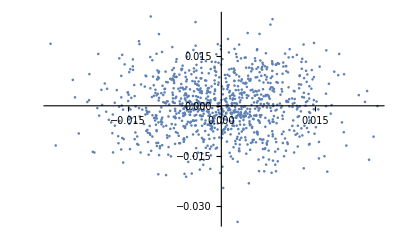

```mathematica
(*A=Transpose[Join[Transpose[coorx[[1;;1000]]],Transpose[coory[[1;;1000]],amplitudep[[1;;1000]]]]];*)
A=Transpose[Join[Transpose[coorx],Transpose[coory],{amplitudep}]];
Take[A,10]
A[[9999]]
ListPlot[A[[;;,{1,2}]]]
ListPlot[A[[;;,{3,4}]]]
ListPlot[A[[;;,{1,3}]]]
```

```mathematica
SetDirectory["C:\\Users\\enrico.felcini\\Desktop\\GIT\\MatLab_3D_Tracking\\Baem_Generation"]
```

C:\Users\enrico.felcini\Desktop\GIT\MatLab_3D_Tracking\Baem_Generation

Just verify that the A matrix is full until end (in case some parts were selected away)

```mathematica
Length[A]
A[[-1]]
```

1000

{0.0139535,0.00109391,-0.00789386,0.000268619,0.}

```mathematica
PartPTC=Table[
StringJoin["ptc_start, x = ",f[-A[[n,1]]-Dx*A[[n,5]],{10,10}],
", px = ",f[-A[[n,2]]-Dxp*A[[n,5]],{10,10}],
", y = ",f[-A[[n,3]]-Dy*A[[n,5]],{10,10}],
", py = ",f[-A[[n,4]]-Dyp*A[[n,5]],{10,10}],
", pt = ",f[A[[n,5]],{10,10}],
";"]
,{n,1,Length[A]}];
AppendTo[PartPTC,"Return;"];
PrependTo[PartPTC,"ptc_start, x = 0.0, px = 0.0, y = 0.0, py = 0.0, pt = 0.0 ;"];
Export["part_PTC_gauss_bx10_ax0_1000.csv",PartPTC,"Table","FieldSeparators"-> ""]
```

part_PTC_gauss_bx10_ax0_1000.csv

```mathematica
"part_PTC_bx10_ax0.txt"
```

part_PTC_bx10_ax0.txt

```mathematica
PartMatlab=Table[
StringJoin[f[A[[n,1]]+Dx*A[[n,5]],{10,10}],
f[A[[n,2]]+Dxp*A[[n,5]],{10,10}],
f[A[[n,3]]+Dy*A[[n,5]],{10,10}],
f[A[[n,4]]+Dyp*A[[n,5]],{10,10}],
f[A[[n,5]],{10,10}]]
,{n,1,Length[A]}];
PrependTo[PartMatlab,"    0.0000000000       0.0000000000       0.0000000000       0.0000000000       0.0000000000"];
PrependTo[PartMatlab,"    x[m]               px[rad]            y[m]               py[rad]            p[?]"];
Export["part_MAT_gauss_bx10_ax0_1000.txt",PartMatlab,"Table","FieldSeparators"-> ""]
```

part_MAT_gauss_bx10_ax0_1000.txt